```mathematica
(* global system *)
(* 
Note ex,ey,ez may vary depending on the person's orientation,
but are currently assumed to be aligned with gravitational vectors
(i.e. flat)
v0 (
*)

ClearAll["Global`*"]
MyTeXForm[a_]:=StringReplace[
StringReplace[ToString[TeXForm[a]],Shortest["\\text{"~~s___~~"}"]->s],
"$"->""]

ex={1,0,0};
ey={0,1,0};
ez={0,0,1};

(* System Parameters *)

(* cup dimensions *)
fv [h_,rb_,rt_]:= (π h)/3(rb^2+rb rt + rt^2) (* frustum volume *)
fcm[h_,rb_,rt_]:= (h(rb^2+2rb rt+ 3 rt^2))/(4(rb^2+rb rt + rt^2))(* frustum centroid *)
fI[h_,rb_,rt_, ρ_]:= ρ 1/60 h π (2 h^2 (rb^2+3 rb rt+6 rt^2)+3 (rb^4+rb^3 rt+rb^2 rt^2+rb rt^3+rt^4)) 
(*
frustum moment,
fI = ρ Integrate[Integrate[Integrate[(z^2+(r Cos[θ])^2)r,{r,0,(rt z)/h + rb(1 - z/h)}],{θ,0,2π}],{z,0,h}];
*)

dlz = 0.093; (* axis offset from bottom *)
ρ = 1000; (* kg/m^3 *)
ch =.18; (* cup height *)
crb = .0582/2; (* cup base *)
crt = .09/2; (* cup top *)
cv = fv[ch,crb,crt]; (* cup volume *)
cm = ρ cv; (* cup mass*)
ccm = fcm[ch,crb,crt]; (* cup centroid *)
cI = fI[ch,crb,crt, ρ] + cm dlz^2; (* cup moment, parallel axis *)
params = {
m -> cm,
lx -> 0.120,
ly -> 0.124,
lz -> ccm - dlz,
g -> 9.81,
Ix -> cI,
Iy -> cI
};

(* person position / velocity *)
p0 = {0,0,0};
v0 = {0,0,0};

(* position / velocity *)
pa = p0 + lx ex + ly Cos[θx] ey + ly Sin[θx] ez;
pb = pa - ly Cos[θx] ey+ lz Sin[θy] ex - lz Cos[θy]ez;
va = v0 + Cross[ωx ex, pa-p0];
vb = Simplify[va + Cross[ωy (-Cos[θx]ey -Sin[θx]ez), pb-pa]];
ω = Transpose[{{ωx ,ωy,0}}];
II = DiagonalMatrix[{Ix,Iy,0}];
(*Print["vb-va"]
MyTeXForm[Transpose[{Simplify[(vb-va)/ωy]}]]*)

p = pb;
v = vb;
(*
p = p0 + (lx + lz Sin[θy])ex + (ly Sin[θx] - lz Cos[θy]) ez;
v= v0 + ωx ly Cos[θx]ez - ωx ly Sin[θx]ey + ωy lz Sin[θy]ez + ωy lz Cos[θy]ex;
*)

(* energy *)
(* TODO : include KE of armature (device) *)
h = Dot[p, ez]
KEl = Simplify[1/2 m Dot[v,v]]
KEω = Simplify[1/2 Dot[ωᵀ,II, ω]][[1,1]]
KE = Simplify[KEl + KEω]
PE = Simplify[m g h]
```

-lz Cos[θy]+ly Sin[θx]

1/2 m (ωy^2 Cos[θx]^2 (lz Cos[θy]-ly Sin[θx])^2+Cos[θx]^2 (ly ωx+lz ωy Sin[θy])^2+Sin[θx]^2 (ly ωx+lz ωy Sin[θy])^2)

1/2 (Ix ωx^2+Iy ωy^2)

1/2 (Ix ωx^2+Iy ωy^2+m (ωy^2 Cos[θx]^2 (lz Cos[θy]-ly Sin[θx])^2+Cos[θx]^2 (ly ωx+lz ωy Sin[θy])^2+Sin[θx]^2 (ly ωx+lz ωy Sin[θy])^2))

g m (-lz Cos[θy]+ly Sin[θx])

```mathematica
(* Lagrangian *)
L = KE-PE
L = L /. {θx -> θx[t], θy -> θy[t]};
L = L /. {ωx -> D[θx[t],t], ωy -> D[θy[t], t]};
Qx=D[(D[L, D[θx[t],t]]), t] - D[L, θx[t]]
Qy=D[(D[L, D[θy[t], t]]), t] - D[L, θy[t]]

sol = Solve[{Qx-τx[t] ==0,Qy - τy[t] ==0}, {θx''[t], θy''[t]}];
δx = Simplify[{θx''[t], θy''[t]}/.sol[[1]]] (* angular acc. *)
```

-g m (-lz Cos[θy]+ly Sin[θx])+1/2 (Ix ωx^2+Iy ωy^2+m (ωy^2 Cos[θx]^2 (lz Cos[θy]-ly Sin[θx])^2+Cos[θx]^2 (ly ωx+lz ωy Sin[θy])^2+Sin[θx]^2 (ly ωx+lz ωy Sin[θy])^2))

g ly m Cos[θx[t]]-1/2 m (-2 ly Cos[θx[t]]^3 (lz Cos[θy[t]]-ly Sin[θx[t]]) θy'[t]^2-2 Cos[θx[t]] Sin[θx[t]] (lz Cos[θy[t]]-ly Sin[θx[t]])^2 θy'[t]^2)+1/2 (2 Ix θx''[t]+m (2 ly Cos[θx[t]]^2 (lz Cos[θy[t]] θy'[t]^2+ly θx''[t]+lz Sin[θy[t]] θy''[t])+2 ly Sin[θx[t]]^2 (lz Cos[θy[t]] θy'[t]^2+ly θx''[t]+lz Sin[θy[t]] θy''[t])))

g lz m Sin[θy[t]]-1/2 m (-2 lz Cos[θx[t]]^2 (lz Cos[θy[t]]-ly Sin[θx[t]]) Sin[θy[t]] θy'[t]^2+2 lz Cos[θx[t]]^2 Cos[θy[t]] θy'[t] (ly θx'[t]+lz Sin[θy[t]] θy'[t])+2 lz Cos[θy[t]] Sin[θx[t]]^2 θy'[t] (ly θx'[t]+lz Sin[θy[t]] θy'[t]))+1/2 (2 Iy θy''[t]+m (-4 Cos[θx[t]] Sin[θx[t]] (lz Cos[θy[t]]-ly Sin[θx[t]])^2 θx'[t] θy'[t]+4 Cos[θx[t]]^2 (lz Cos[θy[t]]-ly Sin[θx[t]]) θy'[t] (-ly Cos[θx[t]] θx'[t]-lz Sin[θy[t]] θy'[t])+2 lz Cos[θx[t]]^2 Cos[θy[t]] θy'[t] (ly θx'[t]+lz Sin[θy[t]] θy'[t])+2 lz Cos[θy[t]] Sin[θx[t]]^2 θy'[t] (ly θx'[t]+lz Sin[θy[t]] θy'[t])+2 Cos[θx[t]]^2 (lz Cos[θy[t]]-ly Sin[θx[t]])^2 θy''[t]+2 lz Cos[θx[t]]^2 Sin[θy[t]] (lz Cos[θy[t]] θy'[t]^2+ly θx''[t]+lz Sin[θy[t]] θy''[t])+2 lz Sin[θx[t]]^2 Sin[θy[t]] (lz Cos[θy[t]] θy'[t]^2+ly θx''[t]+lz Sin[θy[t]] θy''[t])))

{-((-(Iy+m Cos[θx[t]]^2 (lz Cos[θy[t]]-ly Sin[θx[t]])^2+lz^2 m Cos[θx[t]]^2 Sin[θy[t]]^2+lz^2 m Sin[θx[t]]^2 Sin[θy[t]]^2) (-τx[t]+m (g ly Cos[θx[t]]+(ly lz Cos[θx[t]]^2 Cos[θy[t]]+ly lz Cos[θy[t]] Sin[θx[t]]^2+Cos[θx[t]] Sin[θx[t]] (lz Cos[θy[t]]-ly Sin[θx[t]])^2-ly Cos[θx[t]]^3 (-lz Cos[θy[t]]+ly Sin[θx[t]])) θy'[t]^2))+ly lz m Sin[θy[t]] (-τy[t]+m ((-2 ly Cos[θx[t]] Sin[θx[t]]^2 (-2 lz Cos[θy[t]]+ly Sin[θx[t]])+2 ly Cos[θx[t]]^3 (-lz Cos[θy[t]]+ly Sin[θx[t]])-lz^2 Cos[θy[t]]^2 Sin[2 θx[t]]) θx'[t] θy'[t]+lz Sin[θy[t]] (g+Sin[θx[t]] (ly Cos[θx[t]]^2+lz Cos[θy[t]] Sin[θx[t]]) θy'[t]^2))))/(ly^2 lz^2 m^2 Sin[θy[t]]^2-(Ix+ly^2 m) (Iy+m Cos[θx[t]]^2 (lz Cos[θy[t]]-ly Sin[θx[t]])^2+lz^2 m Cos[θx[t]]^2 Sin[θy[t]]^2+lz^2 m Sin[θx[t]]^2 Sin[θy[t]]^2))),(-ly lz m Sin[θy[t]] τx[t]+(Ix+ly^2 m) τy[t]-m (-1/2 (Ix+ly^2 m) Cos[θx[t]] (3 ly lz Cos[2 θx[t]-θy[t]]-2 ly lz Cos[θy[t]]+3 ly lz Cos[2 θx[t]+θy[t]]+2 ly^2 Sin[θx[t]]+2 lz^2 Sin[θx[t]]-2 ly^2 Sin[3 θx[t]]+lz^2 Sin[θx[t]-2 θy[t]]+lz^2 Sin[θx[t]+2 θy[t]]) θx'[t] θy'[t]-1/8 lz Sin[θy[t]] (-8 g (Ix+ly^2 m-ly^2 m Cos[θx[t]])+(ly^2 lz m Cos[θx[t]-θy[t]]+2 lz (Ix+ly^2 m) Cos[2 θx[t]-θy[t]]+3 ly^2 lz m Cos[3 θx[t]-θy[t]]-4 Ix lz Cos[θy[t]]+4 ly^2 lz m Cos[θy[t]]+ly^2 lz m Cos[θx[t]+θy[t]]+2 Ix lz Cos[2 θx[t]+θy[t]]+2 ly^2 lz m Cos[2 θx[t]+θy[t]]+3 ly^2 lz m Cos[3 θx[t]+θy[t]]-2 Ix ly Sin[θx[t]]-2 ly^3 m Sin[θx[t]]+2 ly lz^2 m Sin[2 θx[t]]-2 Ix ly Sin[3 θx[t]]-2 ly^3 m Sin[3 θx[t]]-2 ly^3 m Sin[4 θx[t]]+ly lz^2 m Sin[2 (θx[t]-θy[t])]+ly lz^2 m Sin[2 (θx[t]+θy[t])]) θy'[t]^2)))/(Ix Iy+ly^2 m^2 Cos[θx[t]]^4 (lz Cos[θy[t]]-ly Sin[θx[t]])^2+m Sin[θx[t]]^2 (Iy ly^2+Ix lz^2 Sin[θy[t]]^2)+m Cos[θx[t]]^2 (Iy ly^2+Ix ly^2 Sin[θx[t]]^2+ly^4 m Sin[θx[t]]^4+lz^2 Cos[θy[t]]^2 (Ix+ly^2 m Sin[θx[t]]^2)-2 ly lz Cos[θy[t]] Sin[θx[t]] (Ix+ly^2 m Sin[θx[t]]^2)+Ix lz^2 Sin[θy[t]]^2))}

```mathematica
state = {Ax[t], Ay[t], θx[t], θy[t], θx'[t], θy'[t]};
delta= {θx[t]-1, θy[t]-1, θx'[t], θy'[t], δx[[1]], δx[[2]]} (*against unit step*)
(*
state = {θx[t], θy[t], θx'[t], θy'[t]};
delta= {θx'[t], θy'[t], δx[[1]], δx[[2]]};
*)
input = {τx[t], τy[t]};
output = {θx[t], θy[t]}
sys = NonlinearStateSpaceModel[{delta,output}, state, input];
nsys = sys/.{Ax[t] -> Ax, Ay[t] -> Ay, θx'[t]-> ωx, θy'[t]->ωy, θx[t]->θx, θy[t]->θy, τx[t]->τx, τy[t]->τy}/.params
```

{-1+θx[t],-1+θy[t],θx'[t],θy'[t],-((-(Iy+m Cos[θx[t]]^2 (lz Cos[θy[t]]-ly Sin[θx[t]])^2+lz^2 m Cos[θx[t]]^2 Sin[θy[t]]^2+lz^2 m Sin[θx[t]]^2 Sin[θy[t]]^2) (-τx[t]+m (g ly Cos[θx[t]]+(ly lz Cos[θx[t]]^2 Cos[θy[t]]+ly lz Cos[θy[t]] Sin[θx[t]]^2+Cos[θx[t]] Sin[θx[t]] (lz Cos[θy[t]]-ly Sin[θx[t]])^2-ly Cos[θx[t]]^3 (-lz Cos[θy[t]]+ly Sin[θx[t]])) θy'[t]^2))+ly lz m Sin[θy[t]] (-τy[t]+m ((-2 ly Cos[θx[t]] Sin[θx[t]]^2 (-2 lz Cos[θy[t]]+ly Sin[θx[t]])+2 ly Cos[θx[t]]^3 (-lz Cos[θy[t]]+ly Sin[θx[t]])-lz^2 Cos[θy[t]]^2 Sin[2 θx[t]]) θx'[t] θy'[t]+lz Sin[θy[t]] (g+Sin[θx[t]] (ly Cos[θx[t]]^2+lz Cos[θy[t]] Sin[θx[t]]) θy'[t]^2))))/(ly^2 lz^2 m^2 Sin[θy[t]]^2-(Ix+ly^2 m) (Iy+m Cos[θx[t]]^2 (lz Cos[θy[t]]-ly Sin[θx[t]])^2+lz^2 m Cos[θx[t]]^2 Sin[θy[t]]^2+lz^2 m Sin[θx[t]]^2 Sin[θy[t]]^2))),(-ly lz m Sin[θy[t]] τx[t]+(Ix+ly^2 m) τy[t]-m (-1/2 (Ix+ly^2 m) Cos[θx[t]] (3 ly lz Cos[2 θx[t]-θy[t]]-2 ly lz Cos[θy[t]]+3 ly lz Cos[2 θx[t]+θy[t]]+2 ly^2 Sin[θx[t]]+2 lz^2 Sin[θx[t]]-2 ly^2 Sin[3 θx[t]]+lz^2 Sin[θx[t]-2 θy[t]]+lz^2 Sin[θx[t]+2 θy[t]]) θx'[t] θy'[t]-1/8 lz Sin[θy[t]] (-8 g (Ix+ly^2 m-ly^2 m Cos[θx[t]])+(ly^2 lz m Cos[θx[t]-θy[t]]+2 lz (Ix+ly^2 m) Cos[2 θx[t]-θy[t]]+3 ly^2 lz m Cos[3 θx[t]-θy[t]]-4 Ix lz Cos[θy[t]]+4 ly^2 lz m Cos[θy[t]]+ly^2 lz m Cos[θx[t]+θy[t]]+2 Ix lz Cos[2 θx[t]+θy[t]]+2 ly^2 lz m Cos[2 θx[t]+θy[t]]+3 ly^2 lz m Cos[3 θx[t]+θy[t]]-2 Ix ly Sin[θx[t]]-2 ly^3 m Sin[θx[t]]+2 ly lz^2 m Sin[2 θx[t]]-2 Ix ly Sin[3 θx[t]]-2 ly^3 m Sin[3 θx[t]]-2 ly^3 m Sin[4 θx[t]]+ly lz^2 m Sin[2 (θx[t]-θy[t])]+ly lz^2 m Sin[2 (θx[t]+θy[t])]) θy'[t]^2)))/(Ix Iy+ly^2 m^2 Cos[θx[t]]^4 (lz Cos[θy[t]]-ly Sin[θx[t]])^2+m Sin[θx[t]]^2 (Iy ly^2+Ix lz^2 Sin[θy[t]]^2)+m Cos[θx[t]]^2 (Iy ly^2+Ix ly^2 Sin[θx[t]]^2+ly^4 m Sin[θx[t]]^4+lz^2 Cos[θy[t]]^2 (Ix+ly^2 m Sin[θx[t]]^2)-2 ly lz Cos[θy[t]] Sin[θx[t]] (Ix+ly^2 m Sin[θx[t]]^2)+Ix lz^2 Sin[θy[t]]^2))}

{θx[t],θy[t]}

-1+θx-1+θyωxωy-(-(-τx+0.788158 (1.21644 Cos[θx]+ωy^2 (0.00120031 Cos[θx]^2 Cos[θy]-0.124 Cos[θx]^3 (-0.00967989 Cos[θy]+0.124 Sin[θx])+Cos[θx] (0.00967989 Cos[θy]-0.124 Sin[θx])^2 Sin[θx]+0.00120031 Cos[θy] Sin[θx]^2))) (0.0174445+0.788158 Cos[θx]^2 (0.00967989 Cos[θy]-0.124 Sin[θx])^2+0.0000738506 Cos[θx]^2 Sin[θy]^2+0.0000738506 Sin[θx]^2 Sin[θy]^2)+0.000946031 Sin[θy] (-τy+0.788158 (ωx ωy (0.248 Cos[θx]^3 (-0.00967989 Cos[θy]+0.124 Sin[θx])-0.248 Cos[θx] (-0.0193598 Cos[θy]+0.124 Sin[θx]) Sin[θx]^2-0.0000937003 Cos[θy]^2 Sin[2 θx])+0.00967989 (9.81+ωy^2 Sin[θx] (0.124 Cos[θx]^2+0.00967989 Cos[θy] Sin[θx])) Sin[θy])))/(8.94976×10^-7 Sin[θy]^2-0.0295633 (0.0174445+0.788158 Cos[θx]^2 (0.00967989 Cos[θy]-0.124 Sin[θx])^2+0.0000738506 Cos[θx]^2 Sin[θy]^2+0.0000738506 Sin[θx]^2 Sin[θy]^2))(0.0295633 τy-0.000946031 τx Sin[θy]-0.788158 (-0.00120999 Sin[θy] (-78.48 (0.0295633-0.0121187 Cos[θx])+ωy^2 (0.000117308 Cos[θx-θy]+0.000572338 Cos[2 θx-θy]+0.000351924 Cos[3 θx-θy]-0.000206213 Cos[θy]+0.000117308 Cos[θx+θy]+0.000572338 Cos[2 θx+θy]+0.000351924 Cos[3 θx+θy]-0.00733169 Sin[θx]+0.000018315 Sin[2 θx]-0.00733169 Sin[3 θx]-0.00300544 Sin[4 θx]+9.15748×10^-6 Sin[2 (θx-θy)]+9.15748×10^-6 Sin[2 (θx+θy)]))-0.0147816 ωx ωy Cos[θx] (0.00360092 Cos[2 θx-θy]-0.00240061 Cos[θy]+0.00360092 Cos[2 θx+θy]+0.0309394 Sin[θx]-0.030752 Sin[3 θx]+0.0000937003 Sin[θx-2 θy]+0.0000937003 Sin[θx+2 θy])))/(0.000304312+0.00955147 Cos[θx]^4 (0.00967989 Cos[θy]-0.124 Sin[θx])^2+0.788158 Sin[θx]^2 (0.000268227+1.63456×10^-6 Sin[θy]^2)+0.788158 Cos[θx]^2 (0.000268227+0.000268227 Sin[θx]^2+0.000186337 Sin[θx]^4+0.0000937003 Cos[θy]^2 (0.0174445+0.0121187 Sin[θx]^2)-0.00240061 Cos[θy] Sin[θx] (0.0174445+0.0121187 Sin[θx]^2)+1.63456×10^-6 Sin[θy]^2))θxθyAxAyθxθyωxωy 6222NoneNoneFalseFalseFalse{τx,τy}Automatic

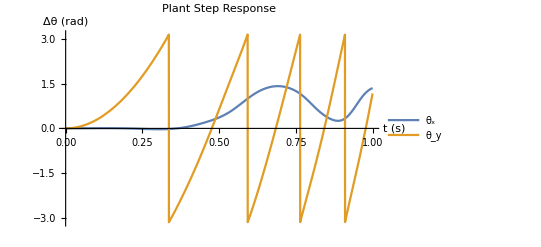

```mathematica
resp = OutputResponse[nsys, {1 * UnitStep[t],1 *UnitStep[t]}, {t,0,1.0}];
respx = resp[[1]];
respx = ArcTan[Cos[respx],Sin[respx]];
respy = resp[[2]];
respy = ArcTan[Cos[respy], Sin[respy]];
Plot[{respx, respy},{t,0,1},  PlotLegends->{"θ_x","θ_y"}, AxesLabel->{"t (s)","Δθ (rad)"}, PlotLabel->"Plant Step Response"]
```

```mathematica
(* Pole Placement *)
(*kpole = StateFeedbackGains[nsys,{-16+3I,-16-3I, -17+5I, -17-5I}]*)

(* LQR Controller *)
qcost = DiagonalMatrix[{1, 1, 1, 1, 1*^-1, 1*^-1}];
(*qcost = DiagonalMatrix[{ 1, 1, 1*^-1, 1*^-1}];*)

qycost = DiagonalMatrix[{1,1}];
rcost = DiagonalMatrix[{.1, .1}];
(*klqr = LQOutputRegulatorGains[nsys,{qycost, rcost}]*)(* τx, τy*)
klqr = LQRegulatorGains[nsys,{qcost, rcost}] (* τx, τy*)
kmat = TraditionalForm[Normal@CoefficientArrays[klqr,{Ax, Ay, θx,θy,ωx,ωy}][[2]]]
TraditionalForm[qcost]
TraditionalForm[rcost]
```

{0.+3.16228 Ax+4.12972 θx+1.11543 ωx,0.+3.16228 Ay+4.04977 θy+1.06859 ωy}

(3.16228 | 0 | 4.12972 | 0 | 1.11543 | 0
0 | 3.16228 | 0 | 4.04977 | 0 | 1.06859)

(1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1/10 | 0
0 | 0 | 0 | 0 | 0 | 1/10)

(0.1 | 0.
0. | 0.1)

{1.,0.99978}

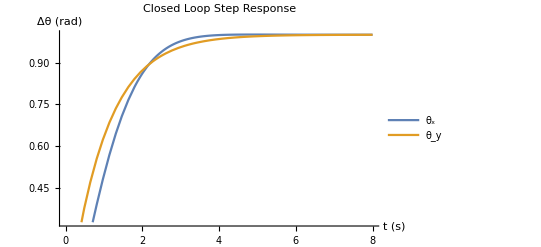

Part::partw: Part 2 of ref[0.000163429] does not exist.

Part::partw: Part 2 of ref[0.163429] does not exist.

Part::partw: Part 2 of ref[0.326694] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

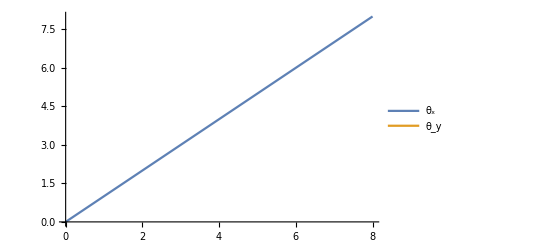

```mathematica
(* Closed-Loop Analysis *)
tlim = 8;
k =klqr;
nsyscl = SystemsModelStateFeedbackConnect[nsys, k];
ref[t] = 1*{UnitStep[t], UnitStep[t]};
rcl = OutputResponse[nsyscl, ref[t], {t,0,tlim}];
rcl/.{t->tlim} (* final value ... *)

Plot[rcl,{t,0,tlim},  PlotLegends->{"θ_x","θ_y"}, AxesLabel->{"t (s)","Δθ (rad)"}, PlotLabel->"Closed Loop Step Response"]
Plot[{ref[t][[1]], ref[t][[2]]},{t,0,tlim}, PlotLegends->{"θ_x","θ_y"}]
(*
ctrl = PIDTune[nsys, {"PID", Automatic}];
nsyscl = PIDTune[nsys, {"PID", Automatic}, "ReferenceOutput"];
(*nsysol = SystemsModelSeriesConnect[ctrl, nsys];
nsyscl = SystemsModelFeedbackConnect[nsysol, -1];
*)

respcl = OutputResponse[nsyscl, UnitStep[t], {t,0,10}];
Plot[%,{t,0,10}]*)
```

```mathematica
(* Jacobian ...*)
(*Jx = Simplify[D[δx, {{θx[t], θy[t]}}]]
Ju = Simplify[D[δx, {{τx[t], τy[t]}}]]

Simplify[Jx/.{θx[t]->0, θy[t]->0 , τx[t]-> 0, τy[t]->0 }]
Simplify[Ju/.{θx[t]->0, θy[t]->0 , τx[t]-> 0, τy[t]->0 }]*)

(* linearization *)
(*ldx = Series[δx, {θx[t], 0, 1}, {θy[t], 0, 1}] // Normal
LaplaceTransform[ldx,t,s]*)
```

```mathematica
(* Pretty *)

MyTeXForm[a_]:=StringReplace[
StringReplace[ToString[TeXForm[a]],Shortest["\\text{"~~s___~~"}"]->s],
{"$"->"", "\\left" -> "", "\\right" -> ""}]

unpretty = {
θx -> θx[t], θy -> θy[t],
ωx -> D[θx[t],t], ωy -> D[θy[t], t]
};
pretty = {
lx-> Subscript[l, x], ly-> Subscript[l, y], lz-> Subscript[l, z],
θx[t] -> Subscript[θ, x], D[θx[t],t] -> Subscript[ω, x], D[D[θx[t],t],t] -> Subscript[α, x],
θy[t] -> Subscript[θ, y], D[θy[t],t] -> Subscript[ω, y], D[D[θy[t],t],t] -> Subscript[α, y],
τx[t]-> Subscript[τ, x] ,τy[t] -> Subscript[τ, y] 
};

(*TraditionalForm[Simplify[Qx/.pretty]]
TraditionalForm[Simplify[Qy/.pretty]]
TraditionalForm[Simplify[δx/.pretty]]
TraditionalForm[Simplify[ldx/.pretty]]*)

ex = Simplify[δx[[1]]/.pretty];
MyTeXForm[ex]

ex = Simplify[δx[[2]]/.pretty];
MyTeXForm[ex]

(*MyTeXForm[Simplify[δx[[1]]/.pretty]]
MyTeXForm[Simplify[δx[[2]]/.pretty]]*)

(* ... *)
Qx/.params;
Qy/.params;
```

-\frac{m l_y l_z \sin (\theta _y) (m (l_z \sin (\theta _y) (g+\sin (\theta _x) (
\begin{array}{c}
 \omega x \\
 \omega y \\
 0 \\
\end{array}
)_y^2 (l_y \cos ^2(\theta _x)+l_z \sin (\theta _x) \cos (\theta _y)))+\frac{1}{2} (
\begin{array}{c}
 \omega x \\
 \omega y \\
 0 \\
\end{array}
)_x (
\begin{array}{c}
 \omega x \\
 \omega y \\
 0 \\
\end{array}
)_y (l_y^2 \sin (4 \theta _x)-l_y l_z (\cos (\theta _x)+3 \cos (3 \theta _x)) \cos (\theta _y)-2 l_z^2 \sin (2 \theta _x) \cos ^2(\theta _y)))-\tau _y)-(Iy+m l_z^2 \sin ^2(\theta _x) \sin ^2(\theta _y)+m l_z^2 \cos ^2(\theta _x) \sin ^2(\theta _y)+m \cos ^2(\theta _x) (l_y \sin (\theta _x)-l_z \cos (\theta _y)){}^2) (m (g l_y \cos (\theta _x)+(
\begin{array}{c}
 \omega x \\
 \omega y \\
 0 \\
\end{array}
)_y^2 (-\frac{1}{4} l_y^2 \sin (4 \theta _x)+l_y l_z (-6 \cos (\theta _x)+3 \cos (2 \theta _x)+5) \cos ^2(\frac{\theta _x}{2}) \cos (\theta _y)+l_z^2 \sin (\theta _x) \cos (\theta _x) \cos ^2(\theta _y)))-\tau _x)}{m^2 l_y^2 l_z^2 \sin ^2(\theta _y)-(Ix+m l_y^2) (Iy+m l_z^2 \sin ^2(\theta _x) \sin ^2(\theta _y)+m l_z^2 \cos ^2(\theta _x) \sin ^2(\theta _y)+m \cos ^2(\theta _x) (l_y \sin (\theta _x)-l_z \cos (\theta _y)){}^2)}

\frac{-m (-\frac{1}{2} l_z \sin (\theta _y) (-2 Ix (g+l_z \sin ^2(\theta _x) \cos (\theta _y) (
\begin{array}{c}
 \omega x \\
 \omega y \\
 0 \\
\end{array}
)_y^2)+2 m l_y^2 (g (\cos (\theta _x)-1)+2 l_z \cos ^2(\frac{\theta _x}{2}) \cos (\theta _x) (3 \cos (\theta _x)-2) \cos (\theta _y) (
\begin{array}{c}
 \omega x \\
 \omega y \\
 0 \\
\end{array}
)_y^2)-l_y \sin (2 \theta _x) (
\begin{array}{c}
 \omega x \\
 \omega y \\
 0 \\
\end{array}
)_y^2 (Ix \cos (\theta _x)-m l_z^2 \cos ^2(\theta _y))-4 m l_y^3 (3 \sin (\frac{\theta _x}{2})-2 \sin (\frac{3 \theta _x}{2})+\sin (\frac{5 \theta _x}{2})) \cos ^3(\frac{\theta _x}{2}) (
\begin{array}{c}
 \omega x \\
 \omega y \\
 0 \\
\end{array}
)_y^2)-\frac{1}{2} \cos (\theta _x) (Ix+m l_y^2) (
\begin{array}{c}
 \omega x \\
 \omega y \\
 0 \\
\end{array}
)_x (
\begin{array}{c}
 \omega x \\
 \omega y \\
 0 \\
\end{array}
)_y (2 l_y^2 (\sin (\theta _x)-\sin (3 \theta _x))+2 l_y l_z (3 \cos (2 \theta _x)-1) \cos (\theta _y)+4 l_z^2 \sin (\theta _x) \cos ^2(\theta _y)))+\tau _y (Ix+m l_y^2)-m l_y l_z \tau _x \sin (\theta _y)}{\frac{1}{8} m l_y^2 (-Ix \cos (4 \theta _x)+Ix+8 Iy+8 m l_z^2 \cos ^2(\theta _x) \cos ^2(\theta _y))+Ix (Iy+m l_z^2 (\cos ^2(\theta _x)+\sin ^2(\theta _x) \sin ^2(\theta _y)))-2 Ix m l_y l_z \sin (\theta _x) \cos ^2(\theta _x) \cos (\theta _y)+\frac{1}{4} m^2 l_y^4 \sin ^2(2 \theta _x)-2 m^2 l_y^3 l_z \sin (\theta _x) \cos ^2(\theta _x) \cos (\theta _y)}

```mathematica
δx
TraditionalForm[Subscript[α, y] == Simplify[δx[[2]]/.pretty]]
```

{-((-(Iy+m Cos[θx[t]]^2 (lz Cos[θy[t]]-ly Sin[θx[t]])^2+lz^2 m Cos[θx[t]]^2 Sin[θy[t]]^2+lz^2 m Sin[θx[t]]^2 Sin[θy[t]]^2) (-τx[t]+m (g ly Cos[θx[t]]+(ly lz Cos[θx[t]]^2 Cos[θy[t]]+ly lz Cos[θy[t]] Sin[θx[t]]^2+Cos[θx[t]] Sin[θx[t]] (lz Cos[θy[t]]-ly Sin[θx[t]])^2-ly Cos[θx[t]]^3 (-lz Cos[θy[t]]+ly Sin[θx[t]])) θy'[t]^2))+ly lz m Sin[θy[t]] (-τy[t]+m ((-2 ly Cos[θx[t]] Sin[θx[t]]^2 (-2 lz Cos[θy[t]]+ly Sin[θx[t]])+2 ly Cos[θx[t]]^3 (-lz Cos[θy[t]]+ly Sin[θx[t]])-lz^2 Cos[θy[t]]^2 Sin[2 θx[t]]) θx'[t] θy'[t]+lz Sin[θy[t]] (g+Sin[θx[t]] (ly Cos[θx[t]]^2+lz Cos[θy[t]] Sin[θx[t]]) θy'[t]^2))))/(ly^2 lz^2 m^2 Sin[θy[t]]^2-(Ix+ly^2 m) (Iy+m Cos[θx[t]]^2 (lz Cos[θy[t]]-ly Sin[θx[t]])^2+lz^2 m Cos[θx[t]]^2 Sin[θy[t]]^2+lz^2 m Sin[θx[t]]^2 Sin[θy[t]]^2))),(-ly lz m Sin[θy[t]] τx[t]+(Ix+ly^2 m) τy[t]-m (-1/2 (Ix+ly^2 m) Cos[θx[t]] (3 ly lz Cos[2 θx[t]-θy[t]]-2 ly lz Cos[θy[t]]+3 ly lz Cos[2 θx[t]+θy[t]]+2 ly^2 Sin[θx[t]]+2 lz^2 Sin[θx[t]]-2 ly^2 Sin[3 θx[t]]+lz^2 Sin[θx[t]-2 θy[t]]+lz^2 Sin[θx[t]+2 θy[t]]) θx'[t] θy'[t]-1/8 lz Sin[θy[t]] (-8 g (Ix+ly^2 m-ly^2 m Cos[θx[t]])+(ly^2 lz m Cos[θx[t]-θy[t]]+2 lz (Ix+ly^2 m) Cos[2 θx[t]-θy[t]]+3 ly^2 lz m Cos[3 θx[t]-θy[t]]-4 Ix lz Cos[θy[t]]+4 ly^2 lz m Cos[θy[t]]+ly^2 lz m Cos[θx[t]+θy[t]]+2 Ix lz Cos[2 θx[t]+θy[t]]+2 ly^2 lz m Cos[2 θx[t]+θy[t]]+3 ly^2 lz m Cos[3 θx[t]+θy[t]]-2 Ix ly Sin[θx[t]]-2 ly^3 m Sin[θx[t]]+2 ly lz^2 m Sin[2 θx[t]]-2 Ix ly Sin[3 θx[t]]-2 ly^3 m Sin[3 θx[t]]-2 ly^3 m Sin[4 θx[t]]+ly lz^2 m Sin[2 (θx[t]-θy[t])]+ly lz^2 m Sin[2 (θx[t]+θy[t])]) θy'[t]^2)))/(Ix Iy+ly^2 m^2 Cos[θx[t]]^4 (lz Cos[θy[t]]-ly Sin[θx[t]])^2+m Sin[θx[t]]^2 (Iy ly^2+Ix lz^2 Sin[θy[t]]^2)+m Cos[θx[t]]^2 (Iy ly^2+Ix ly^2 Sin[θx[t]]^2+ly^4 m Sin[θx[t]]^4+lz^2 Cos[θy[t]]^2 (Ix+ly^2 m Sin[θx[t]]^2)-2 ly lz Cos[θy[t]] Sin[θx[t]] (Ix+ly^2 m Sin[θx[t]]^2)+Ix lz^2 Sin[θy[t]]^2))}

α_y==(-m (-1/2 l_z sin(θ_y) (-2 Ix (g+l_z sin^2(θ_x) cos(θ_y) (ωx
ωy
0)_y^2)+2 m l_y^2 (g (cos(θ_x)-1)+2 l_z cos^2(θ_x/2) cos(θ_x) (3 cos(θ_x)-2) cos(θ_y) (ωx
ωy
0)_y^2)-l_y sin(2 θ_x) (ωx
ωy
0)_y^2 (Ix cos(θ_x)-m l_z^2 cos^2(θ_y))-4 m l_y^3 (3 sin(θ_x/2)-2 sin((3 θ_x)/2)+sin((5 θ_x)/2)) cos^3(θ_x/2) (ωx
ωy
0)_y^2)-1/2 cos(θ_x) (Ix+m l_y^2) (ωx
ωy
0)_x (ωx
ωy
0)_y (2 l_y^2 (sin(θ_x)-sin(3 θ_x))+2 l_y l_z (3 cos(2 θ_x)-1) cos(θ_y)+4 l_z^2 sin(θ_x) cos^2(θ_y)))+τ_y (Ix+m l_y^2)-m l_y l_z τ_x sin(θ_y))/(1/8 m l_y^2 (-Ix cos(4 θ_x)+Ix+8 Iy+8 m l_z^2 cos^2(θ_x) cos^2(θ_y))+Ix (Iy+m l_z^2 (cos^2(θ_x)+sin^2(θ_x) sin^2(θ_y)))-2 Ix m l_y l_z sin(θ_x) cos^2(θ_x) cos(θ_y)+1/4 m^2 l_y^4 sin^2(2 θ_x)-2 m^2 l_y^3 l_z sin(θ_x) cos^2(θ_x) cos(θ_y))

```mathematica
<<ToMatlab`
```

```mathematica
mpretty = {
lx-> lx, ly-> ly, lz-> lz,
θx[t] -> tx, D[θx[t],t] -> wx, D[D[θx[t],t],t] -> ax,
θy[t] -> ty, D[θy[t],t] -> wy, D[D[θy[t],t],t] -> ay,
τx[t]-> ux ,τy[t] -> uy 
};
ToMatlab[δx/.mpretty]
```

[(-1).*(ly.^2.*lz.^2.*m.^2.*sin(ty).^2+(-1).*(Ix+ly.^2.*m).*(Iy+ ...
  m.*cos(tx).^2.*(lz.*cos(ty)+(-1).*ly.*sin(tx)).^2+lz.^2.*m.*cos( ...
  tx).^2.*sin(ty).^2+lz.^2.*m.*sin(tx).^2.*sin(ty).^2)).^(-1).*((-1) ...
  .*((-1).*ux+m.*(g.*ly.*cos(tx)+wy.^2.*(ly.*lz.*cos(tx).^2.*cos(ty) ...
  +ly.*lz.*cos(ty).*sin(tx).^2+cos(tx).*sin(tx).*(lz.*cos(ty)+(-1).* ...
  ly.*sin(tx)).^2+(-1).*ly.*cos(tx).^3.*((-1).*lz.*cos(ty)+ly.*sin( ...
  tx))))).*(Iy+m.*cos(tx).^2.*(lz.*cos(ty)+(-1).*ly.*sin(tx)).^2+ ...
  lz.^2.*m.*cos(tx).^2.*sin(ty).^2+lz.^2.*m.*sin(tx).^2.*sin(ty).^2) ...
  +ly.*lz.*m.*sin(ty).*((-1).*uy+m.*(wx.*wy.*((-2).*ly.*cos(tx).* ...
  sin(tx).^2.*((-2).*lz.*cos(ty)+ly.*sin(tx))+2.*ly.*cos(tx).^3.*(( ...
  -1).*lz.*cos(ty)+ly.*sin(tx))+(-1).*lz.^2.*cos(ty).^2.*sin(2.*tx)) ...
  +lz.*(g+wy.^2.*sin(tx).*(ly.*cos(tx).^2+lz.*cos(ty).*sin(tx))).* ...
  sin(ty)))),(Ix.*Iy+ly.^2.*m.^2.*cos(tx).^4.*(lz.*cos(ty)+(-1).* ...
  ly.*sin(tx)).^2+m.*sin(tx).^2.*(Iy.*ly.^2+Ix.*lz.^2.*sin(ty).^2)+ ...
  m.*cos(tx).^2.*(Iy.*ly.^2+Ix.*ly.^2.*sin(tx).^2+ly.^4.*m.*sin(tx) ...
  .^4+lz.^2.*cos(ty).^2.*(Ix+ly.^2.*m.*sin(tx).^2)+(-2).*ly.*lz.* ...
  cos(ty).*sin(tx).*(Ix+ly.^2.*m.*sin(tx).^2)+Ix.*lz.^2.*sin(ty).^2) ...
  ).^(-1).*((Ix+ly.^2.*m).*uy+(-1).*ly.*lz.*m.*ux.*sin(ty)+(-1).*m.* ...
  ((-1/8).*lz.*sin(ty).*((-8).*g.*(Ix+ly.^2.*m+(-1).*ly.^2.*m.*cos( ...
  tx))+wy.^2.*(ly.^2.*lz.*m.*cos(tx+(-1).*ty)+2.*lz.*(Ix+ly.^2.*m).* ...
  cos(2.*tx+(-1).*ty)+3.*ly.^2.*lz.*m.*cos(3.*tx+(-1).*ty)+(-4).* ...
  Ix.*lz.*cos(ty)+4.*ly.^2.*lz.*m.*cos(ty)+ly.^2.*lz.*m.*cos(tx+ty)+ ...
  2.*Ix.*lz.*cos(2.*tx+ty)+2.*ly.^2.*lz.*m.*cos(2.*tx+ty)+3.*ly.^2.* ...
  lz.*m.*cos(3.*tx+ty)+(-2).*Ix.*ly.*sin(tx)+(-2).*ly.^3.*m.*sin(tx) ...
  +2.*ly.*lz.^2.*m.*sin(2.*tx)+(-2).*Ix.*ly.*sin(3.*tx)+(-2).* ...
  ly.^3.*m.*sin(3.*tx)+(-2).*ly.^3.*m.*sin(4.*tx)+ly.*lz.^2.*m.*sin( ...
  2.*(tx+(-1).*ty))+ly.*lz.^2.*m.*sin(2.*(tx+ty))))+(-1/2).*(Ix+ ...
  ly.^2.*m).*wx.*wy.*cos(tx).*(3.*ly.*lz.*cos(2.*tx+(-1).*ty)+(-2).* ...
  ly.*lz.*cos(ty)+3.*ly.*lz.*cos(2.*tx+ty)+2.*ly.^2.*sin(tx)+2.* ...
  lz.^2.*sin(tx)+(-2).*ly.^2.*sin(3.*tx)+lz.^2.*sin(tx+(-2).*ty)+ ...
  lz.^2.*sin(tx+2.*ty))))];

```mathematica
p
```

{lx+lz Sin[θy],0,-lz Cos[θy]+ly Sin[θx]}

```mathematica
TraditionalForm[
L == T-V]
```

1/2 (Ix (θx'(t))^2+Iy (θy'(t))^2+m (sin^2(θx(t)) (ly θx'(t)+lz θy'(t) sin(θy(t)))^2+cos^2(θx(t)) (ly θx'(t)+lz θy'(t) sin(θy(t)))^2+cos^2(θx(t)) (θy'(t))^2 (lz cos(θy(t))-ly sin(θx(t)))^2))-g m (ly sin(θx(t))-lz cos(θy(t)))==T-V